```mathematica
an=0;
bn=50;
ϵ=10^-4;
h=0.1;
b=1;
a=2;
d=1;
s=-0.1;
c=1;
X[x_,y_]=a*x-(b*x*y)/(1+s*x);
Y[x_,y_]=-c*y+(d*x*y)/(1+s*x);
NN=10000; 
XY=Array[0,{3,NN+1}];
XY[[1,1]]=an;
XY[[2,1]]=1; 
XY[[3,1]]=2;
k=1;
EEmas=Array[0,{2,NN+1}]; 
HH={h};
```

```mathematica
xn=yn=zn=tn=hn=lpx=lpy=lpz={};
AppendTo[xn,1];
AppendTo[yn,2];
```

```mathematica
AppendTo[tn,0];
```

```mathematica
Tsol=Flatten[{x[t],y[t]}/.NDSolve[
{
x'[t]==X[x[t],y[t]],
y'[t]==Y[x[t],y[t]],
x[tn[[1]]]==xn[[1]],
y[tn[[1]]]==yn[[1]]},
{x[t],y[t]},{t,0,bn}
]]
```

{InterpolatingFunction[{{0., 50.}}, <>][t],InterpolatingFunction[{{0., 50.}}, <>][t]}

```mathematica
TX[t_]=Tsol[[1]];
TY[t_]=Tsol[[2]];
```

```mathematica
kkX[h_,Xk_,Yk_]:=FindRoot[{k1x==h X[Xk+1/4 k1x+(1/4-(√3)/6) k2x,Yk+1/4 k1y+(1/4-(√3)/6) k2y],
k1y==h Y[Xk+1/4 k1x+(1/4-(√3)/6) k2x,Yk+1/4 k1y+(1/4-(√3)/6) k2y],
k2x==h X[Xk+(1/4+(√3)/6) k1x+1/4 k2x,Yk+(1/4+(√3)/6) k1y+1/4 k2y],
k2y==h Y[Xk+(1/4+(√3)/6) k1x+1/4 k2x,Yk+(1/4+(√3)/6) k1y+1/4 k2y]

},{k1x,0},{k1y,0},{k2x,0},{k2y,0}];
```

```mathematica
Dynamic[k]
Dynamic[HH[[k]]]
Dynamic[XY[[2,k]]]
Dynamic[XY[[3,k]]]
```

```mathematica
While[XY[[1,k]]≤bn,
{k1xh=kkX[h,XY[[2,k]],XY[[3,k]]][[1,2]];
k1yh=kkX[h,XY[[2,k]],XY[[3,k]]][[2,2]];
k2xh=kkX[h,XY[[2,k]],XY[[3,k]]][[3,2]];
k2yh=kkX[h,XY[[2,k]],XY[[3,k]]][[4,2]];
Yh={XY[[2,k]]+1/2(k1xh+k2xh),XY[[3,k]]+1/2(k1yh+k2yh)};(*шаг аш*)
k1xh2=kkX[h/2,XY[[2,k]],XY[[3,k]]][[1,2]];
k1yh2=kkX[h/2,XY[[2,k]],XY[[3,k]]][[2,2]];
k2xh2=kkX[h/2,XY[[2,k]],XY[[3,k]]][[3,2]];
k2yh2=kkX[h/2,XY[[2,k]],XY[[3,k]]][[4,2]];
Yh2={XY[[2,k]]+1/2(k1xh2+k2xh2),XY[[3,k]]+1/2(k1yh2+k2yh2)};
k1xh3=kkX[h/2,Yh2[[1]],Yh2[[2]]][[1,2]];
k1yh3=kkX[h/2,Yh2[[1]],Yh2[[2]]][[2,2]];
k2xh3=kkX[h/2,Yh2[[1]],Yh2[[2]]][[3,2]];
k2yh3=kkX[h/2,Yh2[[1]],Yh2[[2]]][[4,2]];
Yh3={Yh2[[1]]+1/2(k1xh3+k2xh3),Yh2[[2]]+1/2(k1yh3+k2yh3)};
EE=Abs[(Yh-Yh3)/15];
Ek=√(EE[[1]]^2+EE[[2]]^2);
Which[Ek>ϵ,{h=h/2},Ek≤ ϵ/16,{XY[[1,k+1]]=XY[[1,k]]+h; XY[[2,k+1]]=Yh3[[1]],XY[[3,k+1]]=Yh3[[2]];
EEmas[[2,k]]=Ek;HH=AppendTo[HH,h]; h=2h;k=k+1},ϵ/16<Ek≤ ϵ,{XY[[1,k+1]]=XY[[1,k]]+h; XY[[2,k+1]]=Yh3[[1]],XY[[3,k+1]]=Yh3[[2]];
EEmas[[2,k]]=Ek;
HH=AppendTo[HH,h]; k=k+1}];
}]
```

```mathematica
EEmas[[1]]=XY[[1]];
```

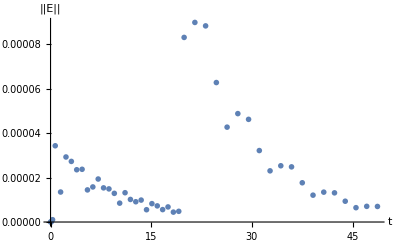

```mathematica
ListPlot[Transpose[EEmas],PlotStyle->PointSize[0.01],AxesLabel->{"t","||E||"}]
```

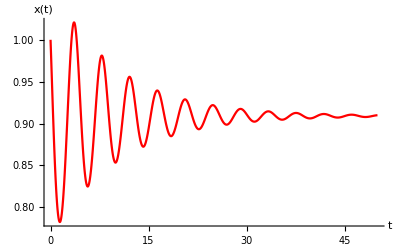

```mathematica
G1=Plot[TX[t],{t,0,bn},PlotStyle->Red,PlotRange->All,AxesLabel->{"t","x(t)"}]
```

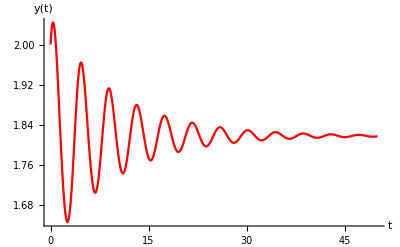

```mathematica
G2=Plot[TY[t],{t,0,bn},PlotStyle->Red,PlotRange->All,AxesLabel->{"t","y(t)"}]
```

```mathematica
m=k-1;
```

```mathematica
Xpogr=Array[0,{m,2}];
```

```mathematica
Do[Xpogr[[k,1]]=XY[[1,k]],{k,1,m}];
```

```mathematica
Do[Xpogr[[k,2]]=Abs[XY[[2,k]]-TX[XY[[1,k]]]],{k,1,m}];
```

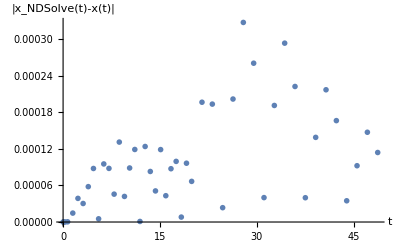

```mathematica
ListPlot[Xpogr,PlotStyle->PointSize[0.01],PlotRange->All,AxesLabel->{"t","|x_NDSolve(t)-x(t)|"}]
```

```mathematica
Ypogr=Array[0,{m,2}];
```

```mathematica
Do[Ypogr[[k,1]]=XY[[1,k]],{k,1,m}];
```

```mathematica
ListPlot[Ypogr,PlotStyle->PointSize[0.01],PlotRange->All,AxesLabel->{"t","|y_NDSolve(t)-y(t)|"}]
```

-Graphics-

```mathematica
XX={{},{}};
```

```mathematica
XX[[1]]=XY[[1]];
```

```mathematica
XX[[2]]=XY[[2]];
```

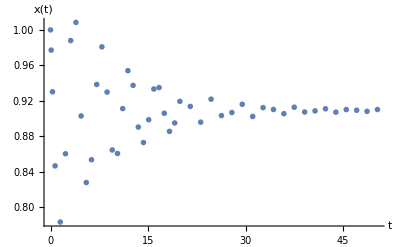

```mathematica
Gr1=ListPlot[Transpose[XX],PlotStyle->PointSize[0.01],AxesLabel->{"t","x(t)"}]
```

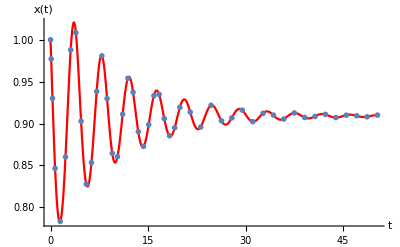

```mathematica
Show[G1,Gr1]
```

```mathematica
YY={{},{}};
```

```mathematica
YY[[1]]=XY[[1]];
```

```mathematica
YY[[2]]=XY[[3]];
```

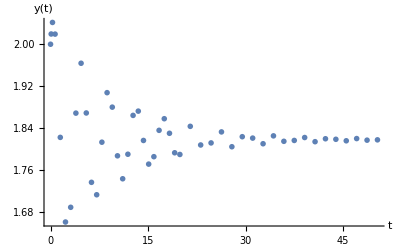

```mathematica
Gr2=ListPlot[Transpose[YY],PlotStyle->PointSize[0.01],AxesLabel->{"t","y(t)"}]
```

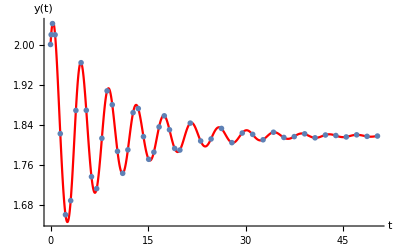

```mathematica
Show[G2,Gr2]
```

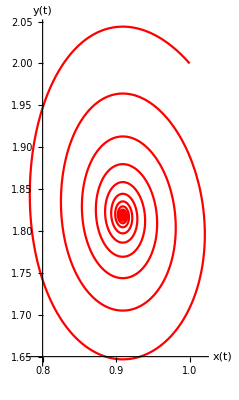

```mathematica
G3=ParametricPlot[{TX[t],TY[t]},{t,0,bn},PlotStyle->Red ,PlotRange->All,AxesLabel->{"x(t)","y(t)"}]
```

```mathematica
Parametr={{},{}};
```

```mathematica
Parametr[[1]]=XY[[2]];
```

```mathematica
Parametr[[2]]=XY[[3]];
```

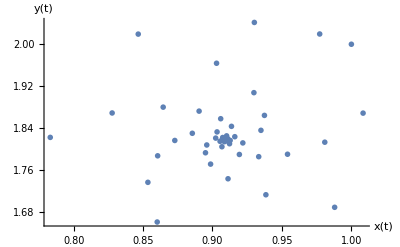

```mathematica
Gr3=ListPlot[Transpose[Parametr],PlotStyle->PointSize[0.01],AxesLabel->{"x(t)","y(t)"}]
```

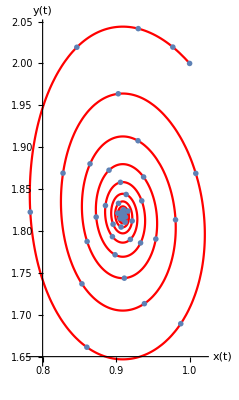

```mathematica
Show[G3,Gr3]
```